```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
benchmarks={"bitonic_2n_float_sort_bench", "bitonic_8n_float_sort_bench","bitonic_float_sort_bench", "std_float_sort_bench", "hybrid_8n_float_sort_bench", "bitonic_float_sort_ver2_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,929769,714.146,714.511,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]//Length  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
data5=GetBenchData[benchmarks[[5]]];
data5=Take[data5, {1, (data5//Length)-2}];
timing5=data5[[All,4]];
NumToSort5=data5[[All,11]];
```

```mathematica
data6=GetBenchData[benchmarks[[6]]];
data6=Take[data6, {1, (data6//Length)-2}];
timing6=data6[[All,4]];
NumToSort6=data6[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First]
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
p5=SortBy[Transpose[{NumToSort5,timing5}], First];
p6=SortBy[Transpose[{NumToSort6,timing6}], First]
```

{{10,744.95},{20,1002.07},{40,1168.12},{50,1575.39},{80,1619.4},{100,2366.31},{200,2983.47},{400,5887.89},{800,12314},{1600,27074.1},{3200,61053.7},{5000,106338},{7500,287310},{10000,234882},{12000,280510},{15000,353868},{17000,452291},{20000,535607},{25000,669724},{27000,712872},{30000,779623},{35000,1.03379×10^6},{40000,1.15098×10^6},{50000,1.43415×10^6},{70000,2.22596×10^6},{100000,3.18578×10^6},{120000,4.40666×10^6},{150000,5.49741×10^6},{200000,7.36786×10^6},{400000,1.63395×10^7},{600000,2.68314×10^7},{800000,3.72748×10^7},{1.×10^6,4.61826×10^7},{1.2×10^6,6.16021×10^7},{1.5×10^6,7.75469×10^7},{1.8×10^6,9.86962×10^7},{2.×10^6,1.05749×10^8},{2.5×10^6,1.45123×10^8},{3.×10^6,1.70793×10^8},{5.×10^6,3.29638×10^8},{7.×10^6,4.51712×10^8},{1.×10^7,6.97182×10^8}}

{{10,738.063},{20,1204.44},{40,1121.1},{50,1647.13},{80,1549.57},{100,2551.05},{200,2912.26},{400,5759},{800,12348.8},{1600,26523.3},{3200,69590.4},{5000,107638},{7500,280115},{10000,232700},{12000,288263},{15000,401010},{17000,482697},{20000,537625},{25000,667718},{27000,701677},{30000,782466},{35000,1.00568×10^6},{40000,1.14184×10^6},{50000,1.46407×10^6},{70000,2.24977×10^6},{100000,3.20978×10^6},{120000,3.89018×10^6},{150000,5.82067×10^6},{200000,7.14467×10^6},{400000,1.62727×10^7},{600000,2.75835×10^7},{800000,3.68546×10^7},{1.×10^6,4.82474×10^7},{1.2×10^6,6.17523×10^7},{1.5×10^6,7.60349×10^7},{1.8×10^6,1.04831×10^8},{2.×10^6,1.16147×10^8},{2.5×10^6,1.52914×10^8},{3.×10^6,1.80588×10^8},{5.×10^6,3.29382×10^8},{7.×10^6,4.49926×10^8},{1.×10^7,7.28357×10^8}}

```mathematica
color=ColorData[10,"ColorList"];
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
{color[[5]], AbsolutePointSize[8]},
{color[[6]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["bitonic 2^n sort", LegendFontSize], Style["bitonic 8n sort", LegendFontSize], Style["bitonic arbitrary n sort", LegendFontSize], 
Style["std sort", LegendFontSize], Style["hybrid 8n sort", LegendFontSize],  Style["bitonic sort ver2", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

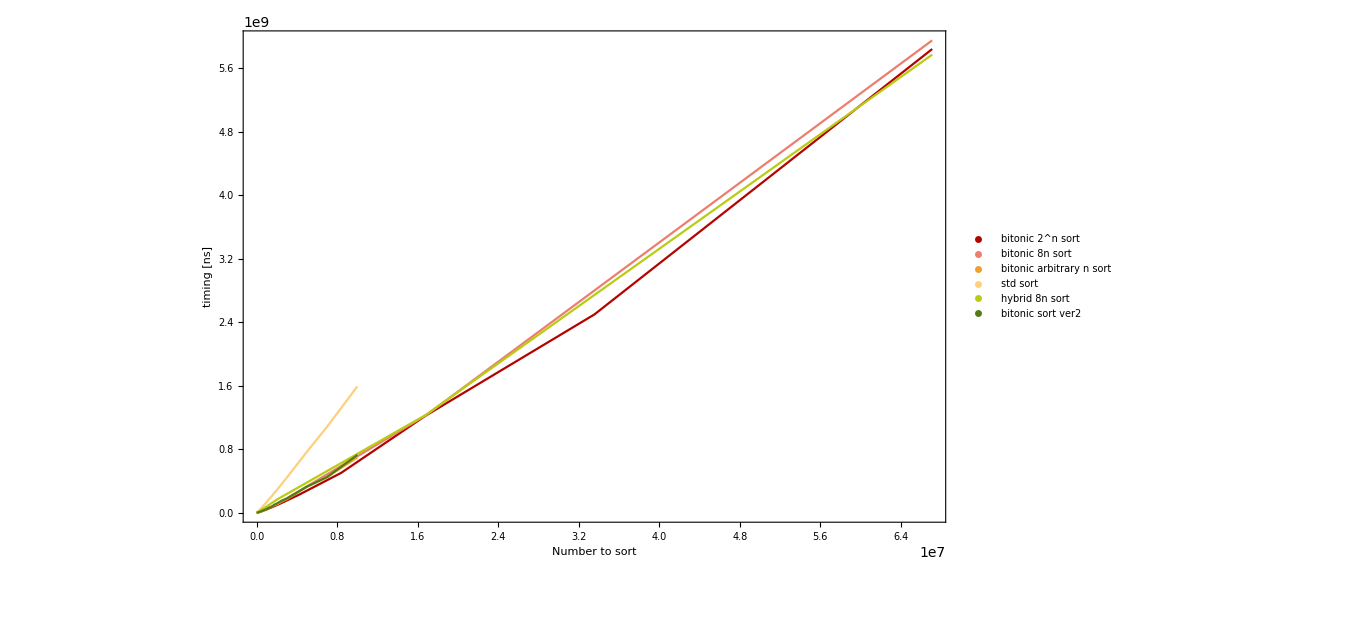

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {1*10^7, 4*10^9}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->All,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

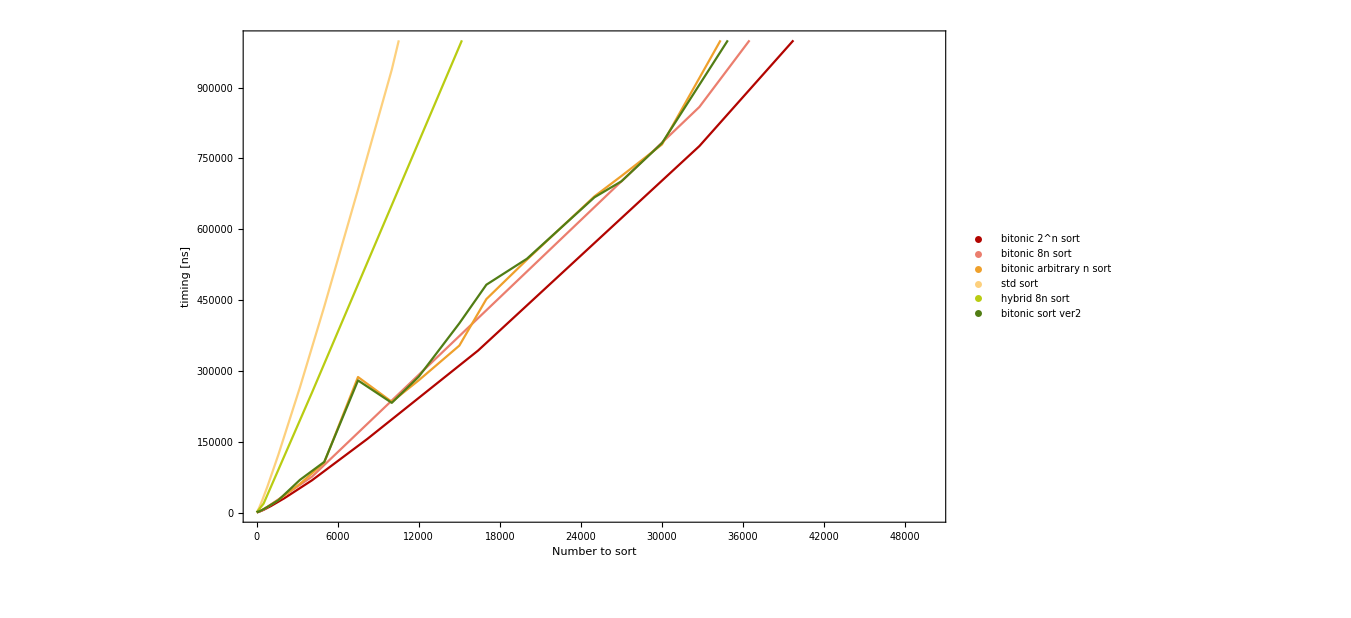

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {4*10^4, 2.2*10^5}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0, 50000},{0, 10 ^6}},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

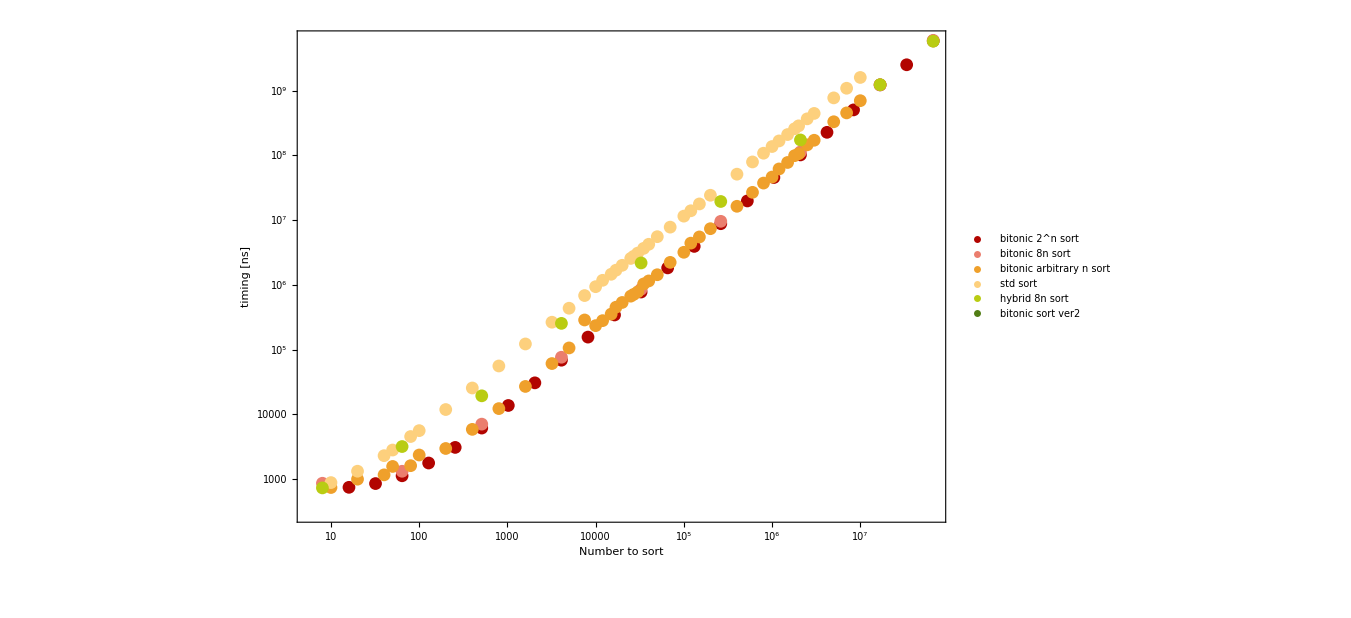

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3,p4, p5
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[37.1976 x+2.73928×10^-7 x^2+0.096705 x Log[x]^2]

FittedModel[-7.66962 x+3.54864×10^-8 x^2+0.289341 x Log[x]^2]

FittedModel[13.1607 x+3.98674×10^-7 x^2+0.201529 x Log[x]^2]

FittedModel[87.8324 x+9.3576×10^-8 x^2+0.270604 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup1=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]//N;
```

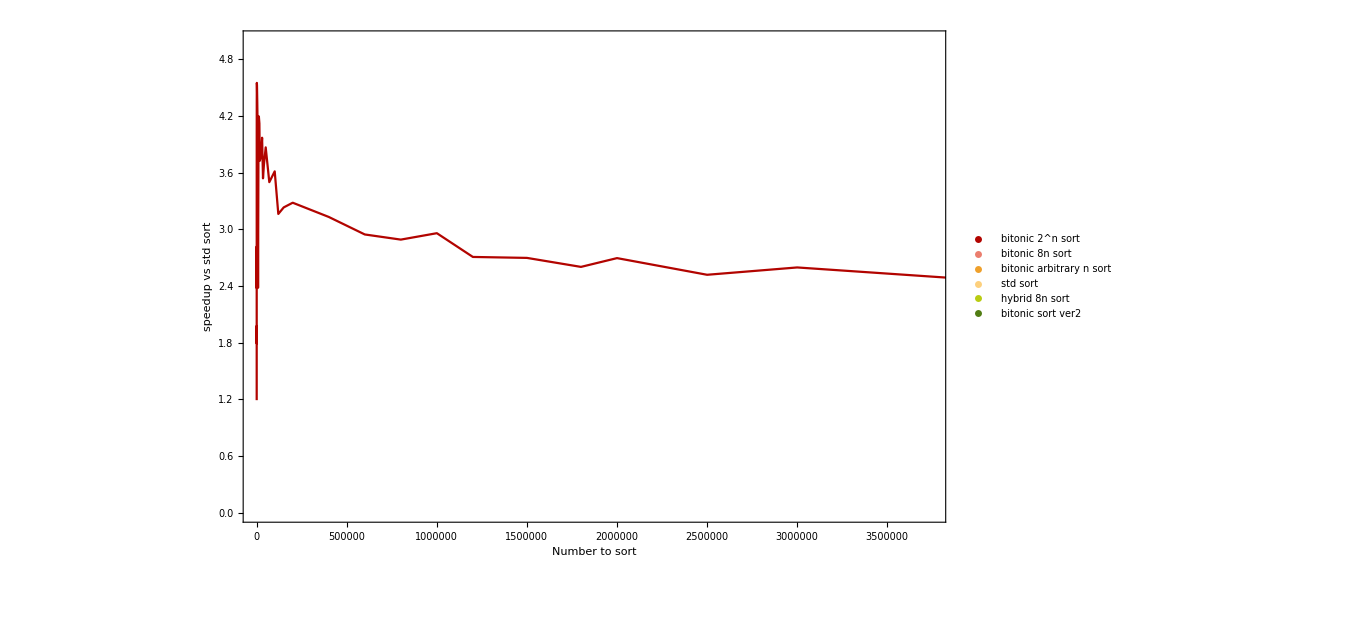

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

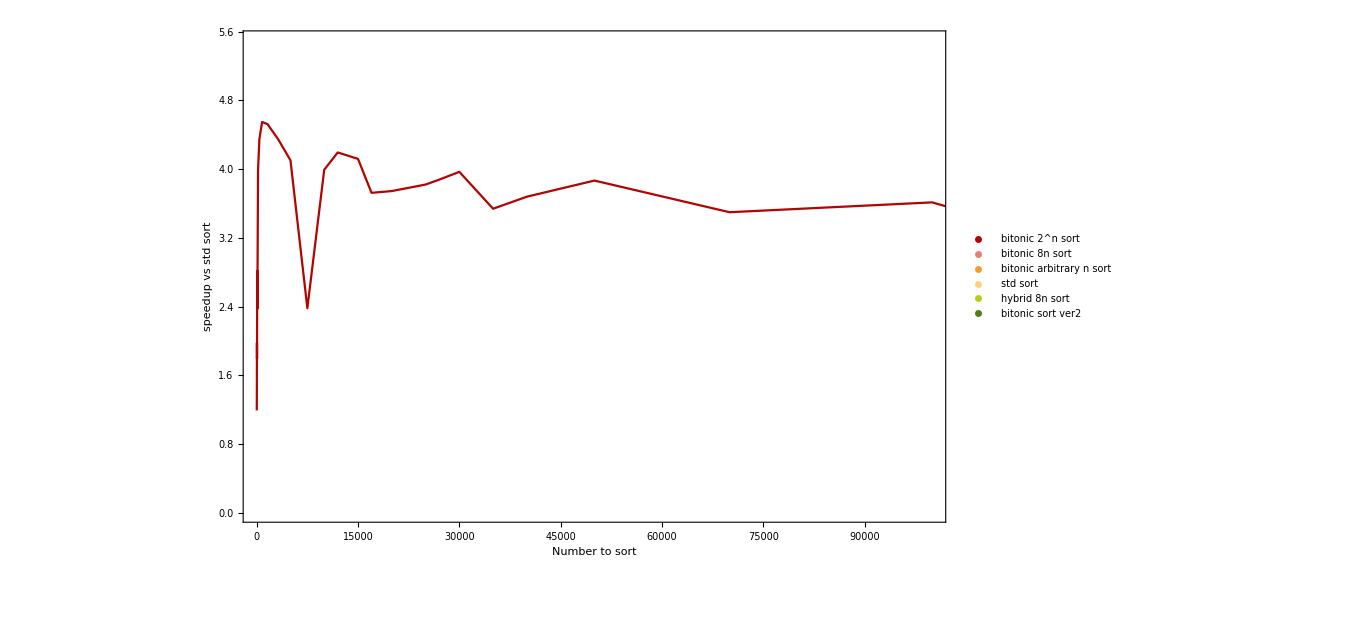

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0,100000},{0,5.5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```